# Energy Minimisation

everything is done in rescaled coordinates so the energy is E/(A*rho*theta^2)

## The inter layer coupling function

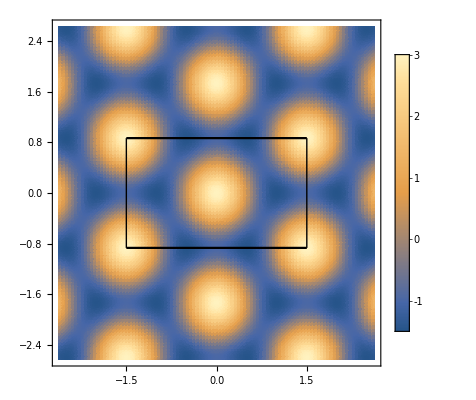

```mathematica
Clear[a,F,x,y,kx,ky]
a=1;
xmax=3*a/(2);
ymax=Sqrt[3]*a/(2);
V=4*ymax*xmax;

q1=2*Pi/a*{-1/3,1/Sqrt[3]};
q2=2*Pi/a*{-1/3,-1/Sqrt[3]};
q3=-(q1+q2);

components={1,1};
rvec=Function[{x,y},{x,y}];
eta=Function[{x,y},Cos[Dot[q1,rvec[x,y]]]+Cos[Dot[q2,rvec[x,y]]]+Cos[Dot[q3,rvec[x,y]]]];
J=Function[{delta,x,y},delta*eta[x,y]];

Plot1=DensityPlot[J[1,x,y],{x,-1.75xmax,1.75 xmax},{y,-1.75xmax,1.75 xmax},PlotLegends->Automatic,PlotPoints->100,FrameTicksStyle->20];
Plot2=Plot[{x=ymax,x=-ymax},{x,-xmax,xmax},PlotStyle->Black,PlotStyle->Thick];
Plot3=Graphics[{Thick,Line[{{-xmax,-ymax},{-xmax,ymax}}],Line[{{xmax,-ymax},{xmax,ymax}}]}];

Show[Plot1,Plot2,Plot3]
DensityPlot[J[1,x,y],{x,-xmax,xmax},{y,-ymax,ymax},PlotLegends->Automatic,PlotPoints->100];
leg1=BarLegend[{"BeachColors",{-1,3}},LabelStyle->Directive[FontSize->20]]
```

check lengths of vectors should be same

```mathematica
Total[q1^2]
Total[q2^2]
Total[q3^2]
```

(16 π^2)/9

(16 π^2)/9

(16 π^2)/9

## The Energy Functional

```mathematica
phiS=Function[{phiS0,phiS1,x,y},phiS0+eta[x,y]*phiS1];
phiA=Function[{phiA0,phiA1,x,y},phiA0+eta[x,y]*phiA1];

phi1=Function[{A0,A1,S0,S1,x,y},1/2*(phiS[S0,S1,x,y]+phiA[A0,A1,x,y])];
phi2=Function[{A0,A1,S0,S1,x,y},1/2*(phiS[S0,S1,x,y]-phiA[A0,A1,x,y])];

gradsq=Function[{phiS1,phiA1},3/8 *Total[q1^2]*((phiS1)^2+(phiA1)^2)];

CosA=Function[{phiA0,phiA1,x,y},Cos[phiA[phiA0,phiA1,x,y]]];
Nlzsq=Function[{phiS0,phiS1,phiA0,phiA1,x,y},Cos[phiS[phiS0,phiS1,x,y]]*Cos[phiS[phiA0,phiA1,x,y]]+1];

Integrand=Function[{d,delta,phiS0,phiS1,phiA0,phiA1,x,y},-d*Nlzsq[phiS0,phiS1,phiA0,phiA1,x,y]-J[delta,x,y]*CosA[phiA0,phiA1,x,y]];

Energy=Function[{d,delta,phiS0,phiS1,phiA0,phiA1,x,y},1/V*(gradsq[phiS1,phiA1]+NIntegrate[Integrand[d,delta,phiS0,phiS1,phiA0,phiA1,x,y],{x,-xmax,xmax},{y,-ymax,ymax}])];

Energy[1,1,1,6,1,6,x,y]
Energy[1,1,1,1,1,1,x,y]
```

89.8108

1.71264

```mathematica
Energy[1,1,-1,-1,-1,-1,x,y]
```

1.71264

```mathematica
1.7126401038451442
```

1.71264

cross check with python to ensure no silly errors

```mathematica
gradsq[0.87,0.32]//N
CosA[0.66,0.15,4.3,8.2]//N
Nlzsq[0.94,0.33,0.53,0.62,3.1,8.1]//N
```

5.65397

0.705684

1.49127

## Energy minimisation

```mathematica
minimisation=Function[{indelta,ind,inphiS0,inphiS1,inphiA0,inphiA1,iters,step,Epoints,inT},
d=ind/(1-ind);
delta=indelta/(1-indelta);

phiS0=inphiS0;
phiS1=inphiS1;
phiA0=inphiA0;
phiA1=inphiA1;

beta=1/inT;
Estep=(iters-1000)/Epoints;

Eold=Energy[d,delta,phiS0,phiS1,phiA0,phiA1,x,y];
Enew=Eold+5;

Eiters={};
S0iters={phiS0};
S1iters={phiS1};
A0iters={phiA0};
A1iters={phiA1};
niters={0};
n=0;
accept=0;
acceptiters={accept};


While[Abs[Eold-Enew]>0,
n=n+1;

DeltaphiS0=phiS0+RandomReal[{-step,step}];
DeltaphiS1=phiS1+RandomReal[{-step,step}];
DeltaphiA0=phiA0+RandomReal[{-step,step}];
DeltaphiA1=phiA1+RandomReal[{-step,step}];

Enew=Energy[d,delta,DeltaphiS0,DeltaphiS1,DeltaphiA0,DeltaphiA1,x,y];
p=Exp[-beta*(Enew-Eold)];
probability=Min[1,p];
random=RandomReal[];
If[ probability>random,{phiS0=DeltaphiS0,phiS1=DeltaphiS1,phiA0=DeltaphiA0,phiA1=DeltaphiA1, If[Eold<Enew,accept=accept+1],Eold=Enew,Enew=2*Eold}];

If[n<=1000 &&  Mod[n,10]==0,{Eiters=Append[Eiters,Eold],S0iters=Append[S0iters,phiS0],S1iters=Append[S1iters,phiS1],A0iters=Append[A0iters,phiA0],A1iters=Append[A1iters,phiA1],niters=Append[niters,n],acceptiters=Append[acceptiters,accept]}];If[n>1000 &&  Mod[n,Estep]==0,{Eiters=Append[Eiters,Eold],S0iters=Append[S0iters,phiS0],S1iters=Append[S1iters,phiS1],A0iters=Append[A0iters,phiA0],A1iters=Append[A1iters,phiA1],niters=Append[niters,n],acceptiters=Append[acceptiters,accept]}];


If[n==iters,{Eold=0,Enew=0}]];

Ef=Mean[Eiters[[-75;;]]];
S0=Mean[S0iters[[-75;;]]];
S1=Mean[S1iters[[-75;;]]];
A0=Mean[A0iters[[-75;;]]];						
A1=Mean[A1iters[[-75;;]]];

Efdev=StandardDeviation[Eiters[[-75;;]]];
S0dev=StandardDeviation[S0iters[[-75;;]]];
S1dev=StandardDeviation[S1iters[[-75;;]]];
A0dev=StandardDeviation[A0iters[[-75;;]]];						
A1dev=StandardDeviation[A1iters[[-75;;]]];];
```

### Collinear State a=0.4 b=0.6

```mathematica
minimisation[0.4,0.6,2,2,2,2,1000,Pi/100,1,0.00075]
accept
```

75

```mathematica
minimisation[0.4,0.6,1,1,1,1,100000,Pi/100,200,0.0007]
EitersC=Eiters;
S0itersC=S0iters;
S1itersC=S1iters;
A0itersC=A0iters;
A1itersC=A1iters;
acceptitersC=acceptiters;

EC=Ef;
S0C=S0
S1C=S1
A0C=A0
A1C=A1
ECdev=Efdev;
S0Cdev=S0dev;
S1Cdev=S1dev;
A0Cdev=A0dev;
A1Cdev=A1dev;
acceptC=accept
```

0.00133022

-0.00078316

-0.00182642

-0.0000633798

12523

```mathematica
ListPlot[EitersC,PlotRange->All,PlotLabel->"energy for parameters alpha=0.4 and beta=0.6",PlotStyle->Black]
ListPlot[S0itersC,PlotRange->All,PlotLabel->"S0 for parameters alpha=0.4 and beta=0.6",PlotStyle->Black,TicksStyle->{Automatic,Opacity[2]},LabelStyle->Opacity[0]]
ListPlot[S1itersC,PlotRange->All,PlotLabel->"S1 for parameters alpha=0.4 and beta=0.6",PlotStyle->Black,TicksStyle->{Automatic,Opacity[2]},LabelStyle->Opacity[0]]
ListPlot[A0itersC,PlotRange->All,PlotLabel->"A0 for parameters alpha=0.4 and beta=0.6",PlotStyle->Black,TicksStyle->{Automatic,Opacity[2]},LabelStyle->Opacity[0]]
ListPlot[A1itersC,PlotRange->All,PlotLabel->"A1 for parameters alpha=0.4 and beta=0.6",PlotStyle->Black,TicksStyle->{Automatic,Opacity[2]},LabelStyle->Opacity[0]]
ListPlot[acceptitersC,PlotRange->All,PlotLabel->"Acceptance through iterations for parameters alpha=0.4 and beta=0.6",AxesLabel->{"iterations","A1"},PlotStyle->Black]
```

```mathematica
S0Cdev=S0dev
S1Cdev=S1dev
A0Cdev=A0dev
A1Cdev=A1dev
```

0.0230628

0.0152408

0.0395467

0.019002

```mathematica
S0Cdev=S0dev
S1Cdev=S1dev
A0Cdev=A0dev
A1Cdev=A1dev
```

0.0230628

0.0152408

0.0395467

0.019002

### Twisted S State a=0.5 b=0.2

```mathematica
minimisation[0.5,0.2,2,2,2,2,1000,Pi/100,1,0.0004]
accept
```

61

```mathematica
minimisation[0.5,0.2,2,2,2,2,100000,Pi/100,200,0.0004]
EitersS=Eiters;
S0itersS=S0iters;
S1itersS=S1iters;
A0itersS=A0iters;
A1itersS=A1iters;
acceptitersS=acceptiters;

ES=Ef;
S0S=S0
S1S=S1
A0S=A0
A1S=A1
ESdev=Efdev;
S0Sdev=S0dev
S1Sdev=S1dev
A0Sdev=A0dev
A1Sdev=A1dev

acceptS=accept
```

3.13755

-0.00101965

2.10197

-0.43033

0.0539436

0.0135397

0.0232444

0.00965687

13880

```mathematica
-2.102622867088529
```

0.0615222

0.0134719

0.0255314

0.0101986

13840

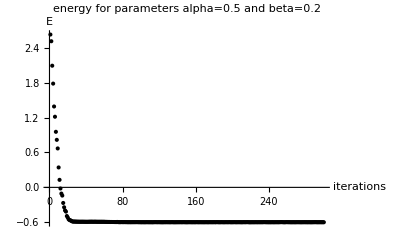

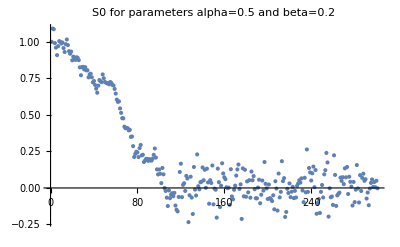

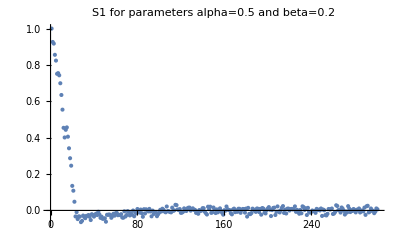

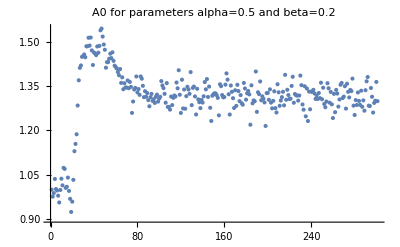

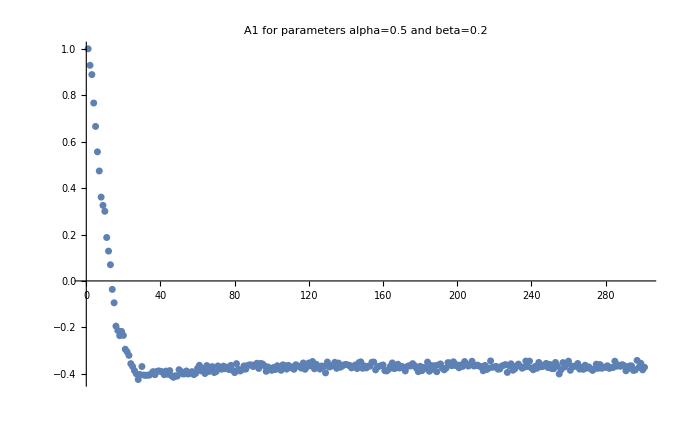

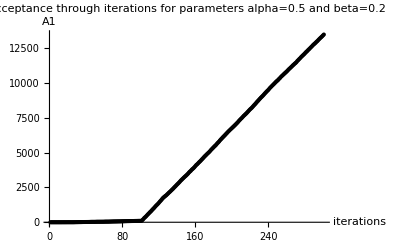

```mathematica
ListPlot[EitersS,PlotRange->All,PlotLabel->"energy for parameters alpha=0.5 and beta=0.2",AxesLabel->{"iterations","E"},PlotStyle->Black]
ListPlot[S0itersS,PlotRange->All,PlotLabel->"S0 for parameters alpha=0.5 and beta=0.2"]
ListPlot[S1itersS,PlotRange->All,PlotLabel->"S1 for parameters alpha=0.5 and beta=0.2"]
ListPlot[A0itersS,PlotRange->All,PlotLabel->"A0 for parameters alpha=0.5 and beta=0.2"]
ListPlot[A1itersS,PlotRange->All,PlotLabel->"A1 for parameters alpha=0.5 and beta=0.2"]
ListPlot[acceptitersS,PlotRange->All,PlotLabel->"Acceptance through iterations for parameters alpha=0.5 and beta=0.2",AxesLabel->{"iterations","A1"},PlotStyle->Black]
```

```mathematica
A1S=A1
```

-0.842514

```mathematica
S0Sdev=S0dev
S1Sdev=S1dev
A0Sdev=A0dev
A1Sdev=A1dev
```

0.0230628

0.0152408

0.0395467

0.019002

### Twisted A State a=0.9 b=0.6

```mathematica
minimisation[0.9,0.6,1,1,1,1,1000,Pi/100,1,0.003]
accept
```

55

```mathematica
minimisation[0.9,0.6,1,1,1,1,100000,Pi/100,200,0.0015]
EitersA=Eiters;
S0itersA=S0iters;
S1itersA=S1iters;
A0itersA=A0iters;
A1itersA=A1iters;
acceptitersA=acceptiters;

EA=Ef;
S0A=S0
S1A=S1
A0A=A0
A1A=A1
acceptA=accept
EAdev=Efdev;
S0Adev=S0dev
S1Adev=S1dev
A0Adev=A0dev
A1Adev=A1dev
```

2.56038

-0.283004

2.03065

-0.842514

11310

0.0722618

0.0315143

0.0141525

0.00798852

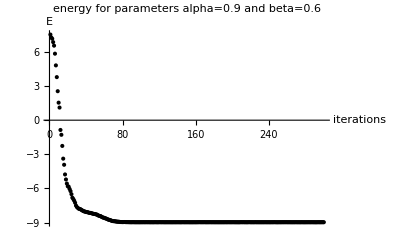

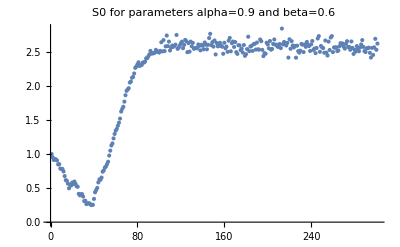

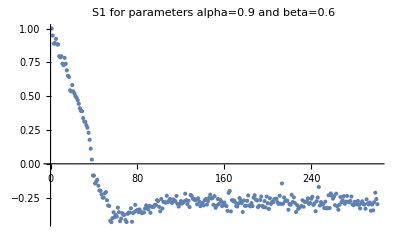

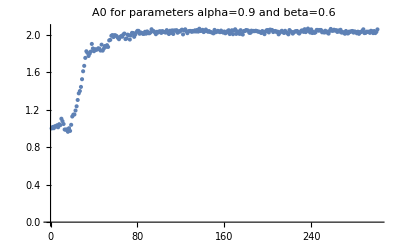

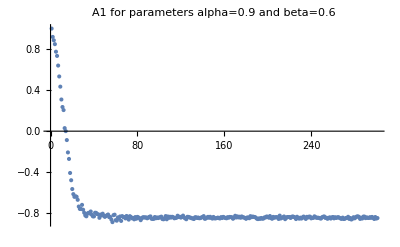

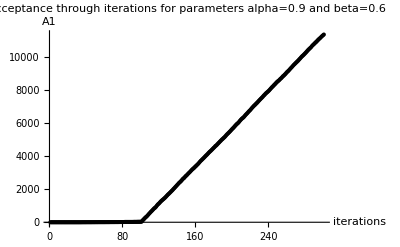

```mathematica
ListPlot[EitersA,PlotRange->All,PlotLabel->"energy for parameters alpha=0.9 and beta=0.6",AxesLabel->{"iterations","E"},PlotStyle->Black]
ListPlot[S0itersA,PlotRange->All,PlotLabel->"S0 for parameters alpha=0.9 and beta=0.6"]
ListPlot[S1itersA,PlotRange->All,PlotLabel->"S1 for parameters alpha=0.9 and beta=0.6"]
ListPlot[A0itersA,PlotRange->All,PlotLabel->"A0 for parameters alpha=0.9 and beta=0.6"]
ListPlot[A1itersA,PlotRange->All,PlotLabel->"A1 for parameters alpha=0.9 and beta=0.6"]
ListPlot[acceptitersA,PlotRange->All,PlotLabel->"Acceptance through iterations for parameters alpha=0.9 and beta=0.6",AxesLabel->{"iterations","A1"},PlotStyle->Black]
```

```mathematica
S0Adev=S0dev
S1Adev=S1dev
A0Adev=A0dev
A1Adev=A1dev
```

0.0230628

0.0152408

0.0395467

0.019002

### real space plots

```mathematica
S0C1=-0.00430999;
S1C1=-0.00831503;
A0C1=-0.0121598;
A1C1=0.00552113;
```

```mathematica
S0S1=-0.0334434;
S1S1=-0.0061743;
A0S1=1.30907;
A1S1=-0.37099;
```

```mathematica
S0A1=2.56833;
S1A1=-0.285746;
A0A1=2.03564;
A1A1=-0.846204;
```

collinear phase

```mathematica
p3=ParametricPlot3D[Table[{i,0,u},{i,0,10}],{u,0,1},Boxed->False,Axes->False,PlotStyle->{Black,Thin,Dashed}];p4=ParametricPlot3D[Table[{10 u,0,i},{i,0,1}],{u,0,1},Boxed->False,Axes->False,PlotStyle->{Black,Thin}];p1=Graphics3D[Table[{Specularity[White,30],Blue,Arrowheads[0.035],Arrow[Tube[{{i,0,0},{i+Sin[phi1[A0C,A1C,S0C,S1C,-3/2+3 i/10,0]],0,Cos[phi1[A0C,A1C,S0C,S1C,-3/2+3 i/10,0]]}},0.04]]},{i,0,10}],Boxed->False];p2=Graphics3D[Table[{Specularity[White,30],Blue,Arrowheads[0.035],Arrow[Tube[{{i,0,1},{i+ Sin[phi2[A0C,A1C,S0C,S1C,-3/2+3 i/10,0]],0,1+Cos[phi2[A0C,A1C,S0C,S1C,-3/2+3 i/10,0]]}},0.04]]},{i,0,10}],Boxed->False];Show[p1,p2,p3,p4,ViewPoint->{0.05,8,0.05}]
```

-Graphics3D-

twisted a phase

```mathematica
p3=ParametricPlot3D[Table[{i,0,u},{i,0,10}],{u,0,1},Boxed->False,Axes->False,PlotStyle->{Black,Thin,Dashed}];p4=ParametricPlot3D[Table[{10 u,0,i},{i,0,1}],{u,0,1},Boxed->False,Axes->False,PlotStyle->{Black,Thin}];p1=Graphics3D[Table[{Specularity[White,30],Blue,Arrowheads[0.035],Arrow[Tube[{{i,0,0},{i+Sin[phi1[A0S,A1S,S0S,S1S,-3/2+3 i/10,0]],0,Cos[phi1[A0S,A1S,S0S,S1S,-3/2+3 i/10,0]]}},0.04]]},{i,0,10}],Boxed->False];p2=Graphics3D[Table[{Specularity[White,30],Blue,Arrowheads[0.035],Arrow[Tube[{{i,0,1},{i+ Sin[phi2[A0S,A1S,S0S,S1S,-3/2+3 i/10,0]],0,1+Cos[phi2[A0S,A1S,S0S,S1S,-3/2+3 i/10,0]]}},0.04]]},{i,0,10}],Boxed->False];Show[p1,p2,p3,p4,ViewPoint->{0.05,8,0.05}]
```

-Graphics3D-

twisted s phase

```mathematica
p3=ParametricPlot3D[Table[{i,0,u},{i,0,10}],{u,0,1},Boxed->False,Axes->False,PlotStyle->{Black,Thin,Dashed}];p4=ParametricPlot3D[Table[{10 u,0,i},{i,0,1}],{u,0,1},Boxed->False,Axes->False,PlotStyle->{Black,Thin}];p1=Graphics3D[Table[{Specularity[White,30],Blue,Arrowheads[0.035],Arrow[Tube[{{i,0,0},{i+Sin[phi1[A0A,A1A,S0A,S1A,-3/2+3 i/10,0]],0,Cos[phi1[A0A,A1A,S0A,S1A,-3/2+3 i/10,0]]}},0.04]]},{i,0,10}],Boxed->False];p2=Graphics3D[Table[{Specularity[White,30],Blue,Arrowheads[0.035],Arrow[Tube[{{i,0,1},{i+ Sin[phi2[A0A,A1A,S0A,S1A,-3/2+3 i/10,0]],0,1+Cos[phi2[A0A,A1A,S0A,S1A,-3/2+3 i/10,0]]}},0.04]]},{i,0,10}],Boxed->False];Show[p1,p2,p3,p4,ViewPoint->{0.05,8,0.05}]
```

-Graphics3D-

```mathematica
Table[-3/2+3 i/10,{i,0,10}]
```

{-3/2,-6/5,-9/10,-3/5,-3/10,0,3/10,3/5,9/10,6/5,3/2}

### Reproducing plot from PNAS of N1.N2

```mathematica
minimisation[0.8,0.8,1,1,1,1,1000,Pi/100,1,0.0018]
accept
```

100

$Aborted

-0.000835647

-0.0018757

0.000898433

-0.00274594

109

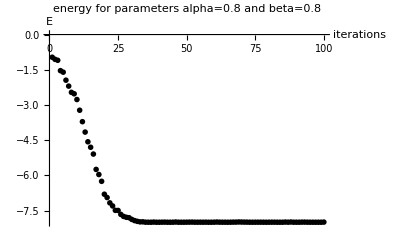

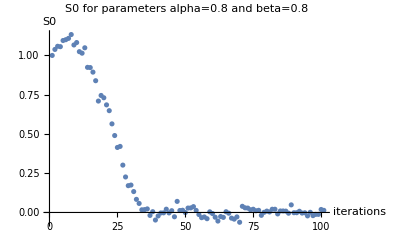

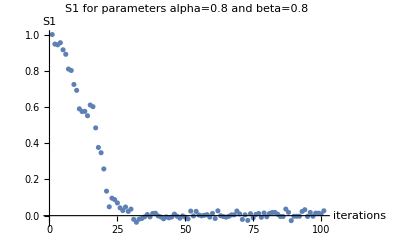

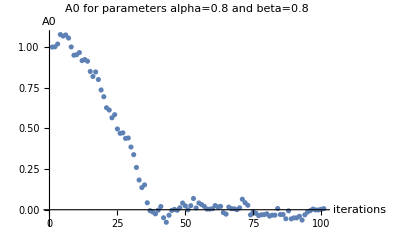

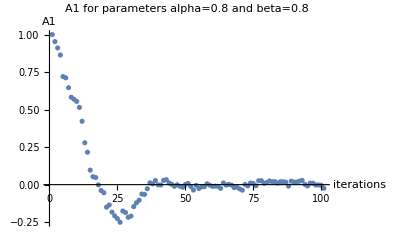

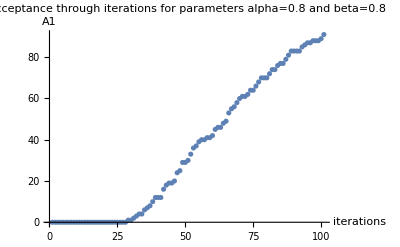

```mathematica
minimisation[0.8,0.8,1,1,1,1,100000,Pi/100,200,0.0018]
EitersP=Eiters;
S0itersP=S0iters;
S1itersP=S1iters;
A0itersP=A0iters;
A1itersP=A1iters;
acceptitersP=acceptiters;

EP=Ef;
S0P=S0
S1P=S1
A0P=A0
A1P=A1
acceptP=accept

ListPlot[EitersP,PlotRange->All,PlotLabel->"energy for parameters alpha=0.8 and beta=0.8",AxesLabel->{"iterations","E"},PlotTheme->"Monochrome"]
ListPlot[S0itersP,PlotRange->All,PlotLabel->"S0 for parameters alpha=0.8 and beta=0.8",AxesLabel->{"iterations","S0"}]
ListPlot[S1itersP,PlotRange->All,PlotLabel->"S1 for parameters alpha=0.8 and beta=0.8",AxesLabel->{"iterations","S1"}]
ListPlot[A0itersP,PlotRange->All,PlotLabel->"A0 for parameters alpha=0.8 and beta=0.8",AxesLabel->{"iterations","A0"}]
ListPlot[A1itersP,PlotRange->All,PlotLabel->"A1 for parameters alpha=0.8 and beta=0.8",AxesLabel->{"iterations","A1"}]
ListPlot[acceptitersP,PlotRange->All,PlotLabel->"Acceptance through iterations for parameters alpha=0.8 and beta=0.8",AxesLabel->{"iterations","A1"}]
```

```mathematica
leg=BarLegend[{"BlueGreenYellow",{0,1}},LabelStyle->Directive[FontSize->24]];
pltM3=MatrixPlot[m,PlotRange->All,PlotLegends->leg1,ColorFunction->(ColorData[{"BlueGreenYellow",{0,1}}]),ColorFunctionScaling->False]
```

```mathematica
leg1=BarLegend[{"BeachColors",{-1,1}},LabelStyle->Directive[FontSize->24]]
```

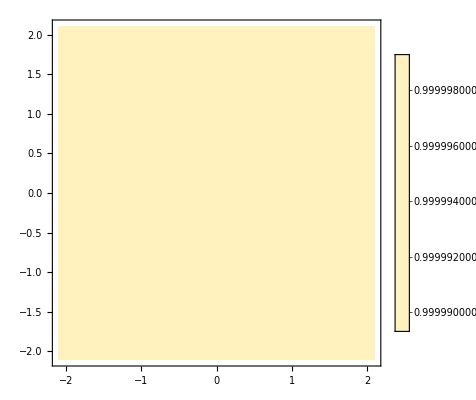

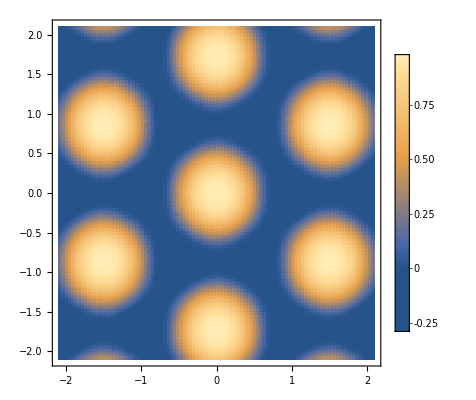

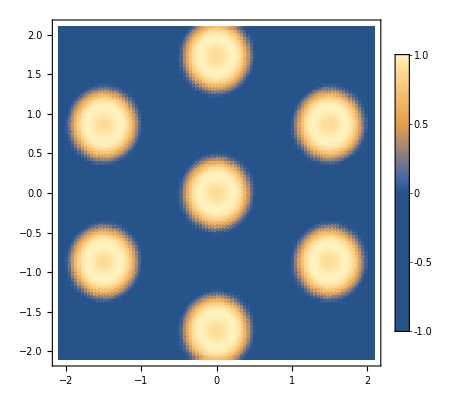

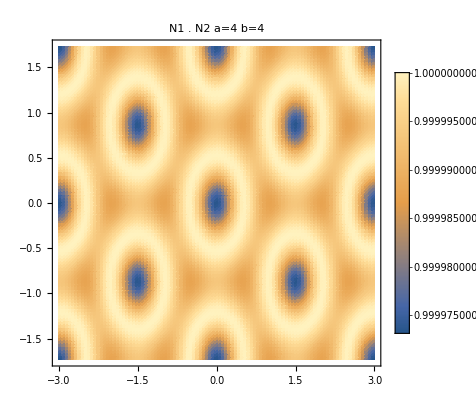

```mathematica
DensityPlot[CosA[A0C,A1C,x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotLegends->Automatic,PlotPoints->100, ColorFunctionScaling->False,FrameTicksStyle->25]
DensityPlot[CosA[A0S,A1S,x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotLegends->Automatic,PlotPoints->100,ColorFunctionScaling->False,FrameTicksStyle->25]
DensityPlot[CosA[A0A,A1A,x,y],{x,-2.1,2.1},{y,-2.1,2.1},PlotLegends->Automatic,PlotPoints->100,ColorFunctionScaling->False,FrameTicksStyle->25]
DensityPlot[CosA[A0P,A1P,x,y],{x,-2xmax,2xmax},{y,-2ymax,2ymax},PlotLegends->Automatic,PlotPoints->100,PlotLabel->"N1 . N2 a=4 b=4"]
```

```mathematica
ColorData
```

{Gradients,Indexed,Named,Physical}

```mathematica
|
```

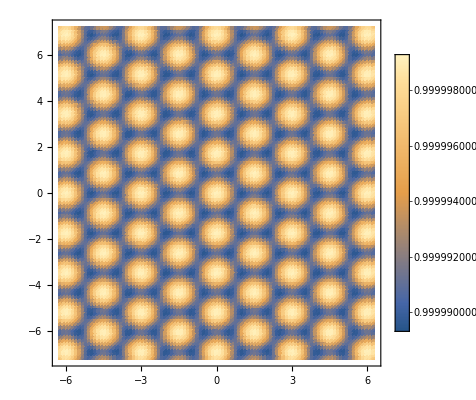

-Graphics-

-Graphics-

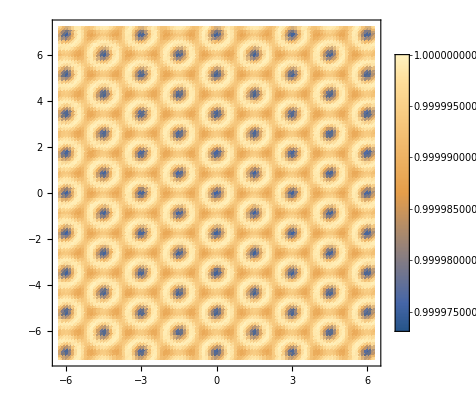

```mathematica
DensityPlot[CosA[A0C,A1C,x,y],{x,-2*Pi,2*Pi},{y,-4*Pi/Sqrt[3],4*Pi/Sqrt[3]},PlotLegends->Automatic,PlotPoints->100]
DensityPlot[CosA[A0S,A1S,x,y],{x,-2*Pi,2*Pi},{y,-4*Pi/Sqrt[3],4*Pi/Sqrt[3]},PlotLegends->Automatic,PlotPoints->100]
DensityPlot[CosA[A0A,A1A,x,y],{x,-2*Pi,2*Pi},{y,-4*Pi/Sqrt[3],4*Pi/Sqrt[3]},PlotLegends->Automatic,PlotPoints->100]
DensityPlot[CosA[A0P,A1P,x,y],{x,-2*Pi,2*Pi},{y,-4*Pi/Sqrt[3],4*Pi/Sqrt[3]},PlotLegends->Automatic,PlotPoints->100]
```